```mathematica
data = Import["/Users/philliphuang/Desktop/d0.xlsx"]
```

{{{128.,29.4864},{256.,50.0568},{512.,83.7285},{1024.,137.461},{2048.,826.975},{4096.,777.26},{8192.,3422.5},{16384.,14021.7},{32768.,47668.3},{65536.,143703.},{131072.,579104.}}}

```mathematica
nlm=NonlinearModelFit[data[[1]],b*x^a,{a,b},x]
```

FittedModel[0.0000580574 x^1.95375]

```mathematica
FittedModel[-0.02838674460300038+0.000013790059349936661 n]
```

FittedModel[-0.0283867+0.0000137901 n]

```mathematica
nlm["BestFit"]
```

0.0000580574 x^1.95375

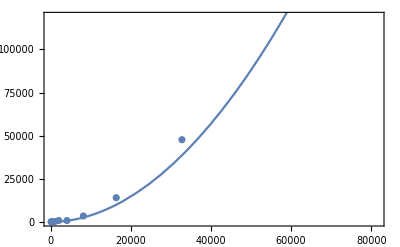

```mathematica
Show[ListPlot[data],Plot[nlm[n],{n,0,150000}],Frame->True]
```

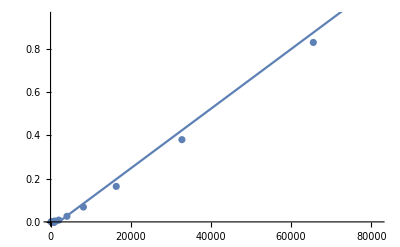

```mathematica
Show[ListPlot[data],Plot[model["BestFit"],{n,0,150000}]]
```

```mathematica
Plot[m["BestFit"],{x,0,150000}]
```

-Graphics-